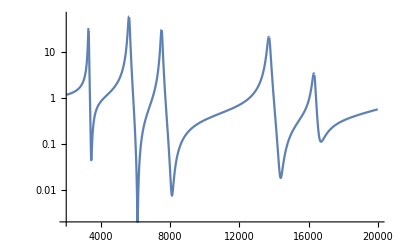

```mathematica
OUTPUTFILENAME="tsequence.csv";
(*Generate some guesses for the transfer function!*)
ωp={3293,5631,7513,13720,16330,28000};
γp=20{1.4,3,3,5,5,5};

ωz={3441.9,6122,8100,14371,16600,42000};
γz={30,21,82,120,200,100};

fnform=(Product[ω-ωz[[j]]-I Abs[γz[[j]]],{j,1,Length[ωz]}]/Product[ω-ωp[[j]]-I Abs[γp[[j]]],{j,1,Length[ωp]}])/(Product[-ωz[[j]]-I Abs[γz[[j]]],{j,1,Length[ωz]}]/Product[-ωp[[j]]-I Abs[γp[[j]]],{j,1,Length[ωp]}])(Product[ω+ωz[[j]]-I Abs[γz[[j]]],{j,1,Length[ωz]}]/Product[ω+ωp[[j]]-I Abs[γp[[j]]],{j,1,Length[ωp]}])/(Product[+ωz[[j]]-I Abs[γz[[j]]],{j,1,Length[ωz]}]/Product[+ωp[[j]]-I Abs[γp[[j]]],{j,1,Length[ωp]}]);

LogPlot[Abs[fnform]^2,{ω,2000,20000}]
```

```mathematica
(*take the IFFT, and plot the result*)
tdat=fnform;
tFIRsample=4.1*10^-6*1.0018;
ωMax=1/(2. tFIRsample);
NsamplesFIR=512*60;(*Number of samples per ram, times number of rams*)
Nsamples=NsamplesFIR*2;(*lets do lots of extra samples just to be safe!*)
ωsample=ωMax/(Nsamples);
sdat=Table[tdat,{ω,-ωMax-ωsample,ωMax,ωsample}];
sdat=Join[Table[tdat,{ω,0,ωMax,ωsample}],Table[tdat,{ω,-ωMax+ωsample,-ωsample,ωsample}]];
fdat=Fourier[sdat];
ListLogPlot[{Abs[Re[fdat]],Abs[Im[fdat]]},PlotRange->All]
```

-Graphics-

```mathematica
datout=#/Max[Abs[#]]&[Re[fdat]];
SetDirectory[NotebookDirectory[]];
Export[OUTPUTFILENAME,datout];(*WE EXPORT MORE VALUES THAN WE SEND AND THEN WE SEND MORE VALUES THAN WE ACTUALLY USE!*)
```